# Sars - Cov - 2 Dynamics

## Reference Model

```mathematica
-Graphics-;
```

## State Dictionary

States to be considered in the AC:

00 - susceptible
01 - no symptoms
02 - moderate symptoms
03 - severe symptoms
04 - critical symptoms
05 - hospitalization
06 - ICU/ventilation
07 - contagious without symptoms
08 - contagious moderate symptoms
09 - contagious severe symptoms
10 - contagious critical symptoms
11 - dead
12 - immune/isolated

## Distributions

Defines some random distribution functions to be used by the model.

```mathematica
acRandom[mean_,dev_]:=Round[(Sqrt[-2*Log[RandomReal[1]]]*Cos[2*Pi*RandomReal[1]])*dev+mean] (* normal distribution *)
```

## Initial Population and Control Grid

Defines the initial population to be analyzed, all with state susceptible, or 0 . The variable n represents the square grid size. In parallel, defines a duration matrix, which will be responsible to store the respective iteraction in which the correspondent cell in the population is. The population is created with a number of isolated/immune cells and one of the susceptible cells is chosen to be patient zero.

```mathematica
createPopulation[n_,immune_]:=ReplacePart[#,RandomChoice[Position[#,0]]->1] &[RandomChoice[If[immune>0,Join[Array[12&,immune],Array[0&,100-immune]],{0}], {n, n}]]
createControl[n_]:=Table[1,{i,n},{j,n}]
```

## States Duration

Defines how many iterations a cell should remain in a state. Since it’s a function, the state duration can be replaced by another function call, allowing to implement state duration conditions.

```mathematica
durations = 
{Infinity,  (* 00 - duration for susceptibles *)
acRandom[5,0.68],    (* 01 - duration for no symptoms *)
acRandom[5,0.68],    (* 02 - duration for moderate symptoms *)
acRandom[4,0.68],    (* 03 - duration for severe symptoms *)
acRandom[3,0.68],    (* 04 - duration for critical symptoms *)
acRandom[12,1.6],  (* 05 - duration for hospitalization *)
acRandom[14,1.8],  (* 06 - duration for ICU/ventilation *)
acRandom[10,1.4],  (* 07 - duration for contagious without symptoms *)
acRandom[15,2.0],  (* 08 - duration for contagious moderate symptoms *)
acRandom[5,0.68],    (* 09 - duration for contagious severe symptoms *)
acRandom[4,0.6],    (* 10 - duration for contagious critical symptoms *)
Infinity,                                   (* 11 - duration for dead *)
Infinity};                                 (* 12 - duration for immune/isolated *)
duration[i_]:=durations⟦i + 1⟧
```

## Contamination Probability

Defines the propability a cell which can contaminate others has to effectivelly do it. Each state has its own probability

```mathematica
probabilities = 
{0,    (* 00 - probability for susceptibles *)
acRandom[81,6],    (* 01 - probability for no symptoms *)
acRandom[81,6],    (* 02 - probability for moderate symptoms *)
acRandom[81,6],    (* 03 - probability for severe symptoms *)
acRandom[81,6],    (* 04 - probability for critical symptoms *)
acRandom[20,6],    (* 05 - probability for hospitalization *)
acRandom[20,6],    (* 06 - probability for ICU/ventilation *)
acRandom[81,6],    (* 07 - probability for contagious without symptoms *)
acRandom[81,6],    (* 08 - probability for contagious moderate symptoms *)
acRandom[81,6],    (* 09 - probability for contagious severe symptoms *)
acRandom[81,6],    (* 10 - probability for contagious critical symptoms *)
0,      (* 11 - probability for dead *)
0};    (* 12 - probability for immune/isolated *)
probability[i_]:=probabilities⟦i +1⟧
```

## Probabilities

Defines some functions to calculate the probability of the next state for specific cases, such as contaminations or immunisations/deaths.

```mathematica
covidType:=RandomChoice[Join[Array[7 &, 30], Array[2 &, 55], Array[3 &, 10], Array[4 &, 5]]]
killOrHealSevere[probability_]:=If[probability>0,RandomChoice[Join[Array[9 &, 100-acRandom[probability,3]], Array[11 &, acRandom[probability,3]]]],9]
killOrHealCritical[probability_]:=If[probability>0,RandomChoice[Join[Array[10 &, 100-acRandom[probability,3]], Array[11 &, acRandom[probability,3]]]],10]
```

## Transitions

Defines the next state for the states based on durations, not the ones based on neighborhood. The susceptible state has no transitions defined here, since the contamination logic is implemented apart. Also increments the iteration in the control grid.

```mathematica
nextState[population_,control_, state_, next_]:=If[control⟦#⟦1⟧,#⟦2⟧⟧≥duration[state],#-> next, #-> state]&/@Position[population, state]
resetControl[population_,control_, state_]:=If[control⟦#⟦1⟧,#⟦2⟧⟧≥duration[state],
#-> 1, #-> control⟦#⟦1⟧,#⟦2⟧⟧+1]&/@Position[population, state] 
next[population_,control_]:=Join[
nextState[population,control, 1, covidType],
nextState[population,control, 2, 8],
nextState[population,control, 3, 5],
nextState[population,control, 4, 6],
nextState[population,control, 5, killOrHealSevere[15]],
nextState[population,control, 6, killOrHealCritical[50]],
nextState[population,control, 7, 12],
nextState[population,control, 8, 12],
nextState[population,control, 9, 12],
nextState[population,control, 10, 12],
nextState[population,control, 12, 0]]
reset[population_, control_]:=Join[
resetControl[population,control, 1],
resetControl[population,control, 2],
resetControl[population,control, 3],
resetControl[population,control, 4],
resetControl[population,control, 5],
resetControl[population,control, 6],
resetControl[population,control, 7],
resetControl[population,control, 8],
resetControl[population,control, 9],
resetControl[population,control, 10],
resetControl[population,control, 12]]
```

## Contamination

Defines the contamination radius and neighborhood format. A contamination probability is taken into account, as well the desired state for which the respective neighbour cells will be contaminated if susceptible.

```mathematica
contaminate[probability_]:=If[probability>0,
If[probability<100,
RandomChoice[Join[Array[0 &, 100-probability], Array[1 &, probability]]],1],0]
contamination[population_, neighbourhood_]:=Thread[
Position[population,0]-> (contaminate[Round[#]]&/@
(Mean[(probability[population⟦#⟦1⟧,#⟦2⟧⟧]&/@#)]&/@(#&/@(Select[#,#⟦1⟧≤Length[population]&&#⟦2⟧≤Length[population]&&#⟦1⟧≥1&&#⟦2⟧≥1&]&/@(neighbourhood+ConstantArray[#,Length[neighbourhood]]&/@Position[population,0])))))]
```

## Stopping Criterion

The simulation must stop when the entire population has achieved immunity or death (cells with value 8 or 9).

```mathematica
shouldStop[population_]:=(Total[Count[#,11]&/@population]+
Total[Count[#,12]&/@population]+
Total[Count[#,0]&/@population])==Length[population]^2
```

## Simulation

Executes the main simulation with the functions defined above. We are first considering the amount of days of iterations instead of a convergent state.

```mathematica
runModel[side_,immunes_]:=Module[{
population,
control,
neighbourhood,
dynamics,
susceptibles,
infected,
immune,
dead,
n,
pop
},
population=createPopulation[side,immunes];
control=createControl[side];
neighbourhood={{1,0},{0,1},{-1,0},{0,-1},{1,1},{1,-1},{-1,1},{-1,-1}};
dynamics={};
susceptibles={};
infected = {};
immune = {};
dead = {};
n=0;
While[!shouldStop[population],
pop = ReplacePart[population,Join[contamination[population,neighbourhood],next[population, control]]];
control = ReplacePart[control,reset[population, control]];
population=pop;
AppendTo[dynamics,population];
AppendTo[susceptibles, 100*(Total[Count[#,0]&/@population])/(side^2)];
AppendTo[infected, 
100*(Total[Count[#,1]&/@population]+
Total[Count[#,2]&/@population]+
Total[Count[#,3]&/@population]+
Total[Count[#,4]&/@population]+
Total[Count[#,5]&/@population]+
Total[Count[#,6]&/@population]+
Total[Count[#,7]&/@population]+
Total[Count[#,8]&/@population]+
Total[Count[#,9]&/@population]+
Total[Count[#,10]&/@population])/(side^2)];
AppendTo[immune, 100*(Total[Count[#,12]&/@population])/(side^2)];
AppendTo[dead, 100*(Total[Count[#,11]&/@population])/(side^2)];
n = n+1;
];
Return[{dynamics, susceptibles, infected, immune, dead}]
]
```

## Execution

Executing the main simulation for test purposes.

Wed 13 Oct 2021 15:20:52GMT-3

Wed 13 Oct 2021 15:22:11GMT-3

230

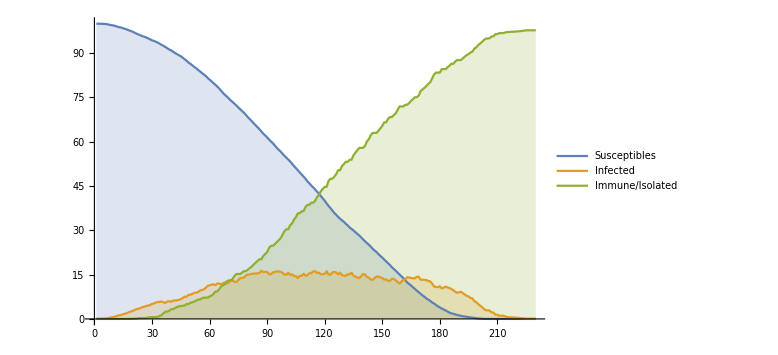

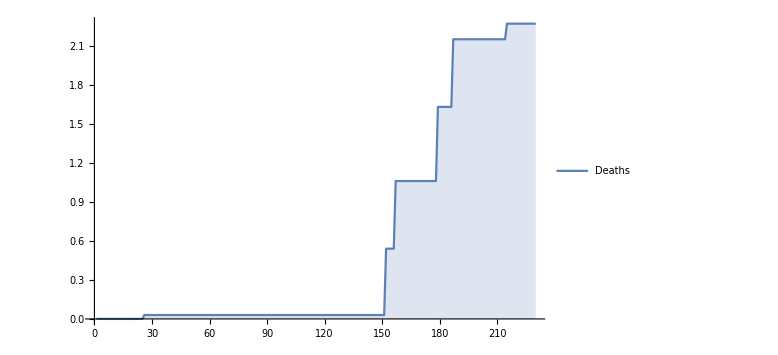

```mathematica
Now
results = runModel[100,0];
Now
dynamics=results⟦1⟧;
susceptibles=results⟦2⟧;
infected=results⟦3⟧;
immune=results⟦4⟧;
dead=results⟦5⟧;
ListAnimate[ArrayPlot[#]&/@dynamics]
ListLinePlot[{
susceptibles,
infected,
immune},
Filling->Axis, 
PlotLegends->{"Susceptibles", "Infected", "Immune/Isolated"},
ImageSize->Large]
ListLinePlot[{
dead},
Filling->Axis, 
PlotLegends->{"Deaths"},
ImageSize->Large]
```

Main simulation: the purpose is to evaluate the impact of the immunity ratio in the metrics purposed.

Wed 27 Oct 2021 13:20:02GMT-3

Wed 27 Oct 2021 17:36:28GMT-3

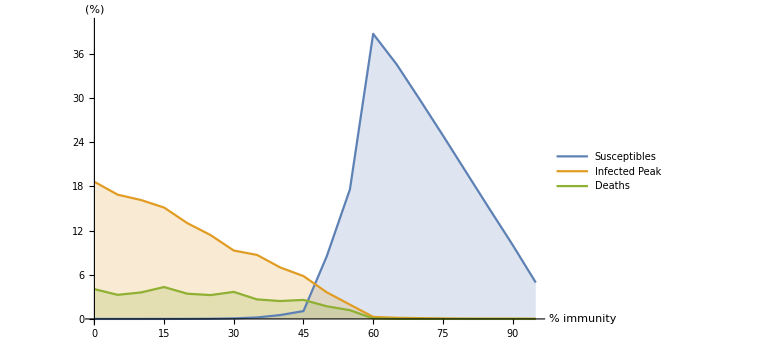

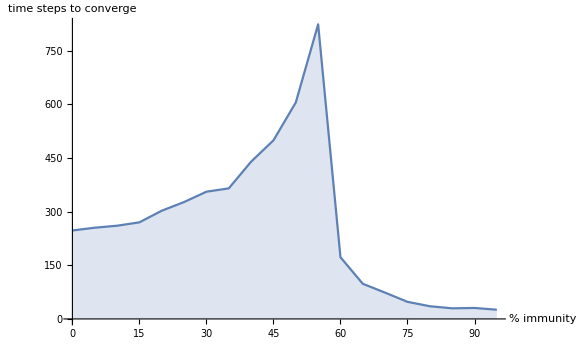

```mathematica
immunity = {0,5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95};
size = 100;
averages = 10; (*Leave to the developer to edit*)
Now
results = Table[runModel[size,#],averages]&/@immunity;
Now
susceptibles=Mean[{Last[#⟦1,2⟧],Last[#⟦2,2⟧],Last[#⟦3,2⟧],Last[#⟦4,2⟧],Last[#⟦5,2⟧],Last[#⟦6,2⟧],Last[#⟦7,2⟧],Last[#⟦8,2⟧],Last[#⟦9,2⟧],Last[#⟦10,2⟧]}]&/@results;
susceptibles = Transpose[{immunity,susceptibles}];
(*ListPlot[{susceptibles}, Filling->Axis, AxesLabel->{"% immunity","% susceptibles not contaminated"},ImageSize->Large]*)
peak=Mean[{Max[#⟦1,3⟧],Max[#⟦2,3⟧],Max[#⟦3,3⟧],Max[#⟦4,3⟧],Max[#⟦5,3⟧],Max[#⟦6,3⟧],Max[#⟦7,3⟧],Max[#⟦8,3⟧],Max[#⟦9,3⟧],Max[#⟦10,3⟧]}]&/@results;
peak = Transpose[{immunity,peak}];
(*ListPlot[{peak}, Filling->Axis, AxesLabel->{"% immunity","% infection peak"},ImageSize->Large]*)
dead=Mean[{Last[#⟦1,5⟧],Last[#⟦2,5⟧],Last[#⟦3,5⟧],Last[#⟦4,5⟧],Last[#⟦5,5⟧],Last[#⟦6,5⟧],Last[#⟦7,5⟧],Last[#⟦8,5⟧],Last[#⟦9,5⟧],Last[#⟦10,5⟧]}]&/@results;
dead = Transpose[{immunity,dead}];
(*ListPlot[{dead}, Filling->Axis, AxesLabel->{"% immunity","% death"},ImageSize->Large]*)
steps=Mean[{Length[#⟦1,1⟧],Length[#⟦2,1⟧],Length[#⟦3,1⟧],Length[#⟦4,1⟧],Length[#⟦5,1⟧],Length[#⟦6,1⟧],Length[#⟦7,1⟧],Length[#⟦8,1⟧],Length[#⟦9,1⟧],Length[#⟦10,1⟧]}]&/@results;
steps = Transpose[{immunity,steps}];
ListLinePlot[{susceptibles, peak,dead}, Filling->Axis, AxesLabel->{"% immunity","(%)"}, PlotLegends->{"Susceptibles", "Infected Peak", "Deaths"},ImageSize->Large, PlotRange->{{0,95},{0,40}}]
ListLinePlot[{steps}, Filling->Axis, AxesLabel->{"% immunity","time steps to converge"},ImageSize->Large]
```